## Жук В. А.

## Лабораторная работа №5 : Численные расчёты в системе Mathematica

## 5.1

#### 5.1.а | Пробел выполняет роль знака умножения

```mathematica
6 4
```

24

#### 5.1.б | Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
6   4
```

24

```mathematica
13+               7
```

20

#### 5.1.в | Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя

```mathematica
1/3
```

1/3

```mathematica
5^(1/2)
```

√5

#### 5.1.г | Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды

```mathematica
1/3.
```

0.333333

```mathematica
5.^(1/2)
```

2.23607

#### 5.1.д | Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
6   (7-1)
```

36

## 5.2

#### 5.2.а | С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17],200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

#### 5.2.б | Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа

```mathematica
N[E^(Pi*Sqrt[163]),40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[N[E^(Pi*Sqrt[163]),40]] - N[E^(Pi*Sqrt[163]),40]
```

7.499274028×10^-13

#### 5.2.в | Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

#### 5.2.г | Последовательно введите выражения | Справедливо ли неравенство

```mathematica
5>3
```

True

```mathematica
5<2
```

False

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E]
```

22.4592

```mathematica
N[E^Pi]
```

23.1407

## 5.3

#### 5.3.а | Решить уравнения

```mathematica
NSolve[Sqrt[x+2]+4*x==4,x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

#### 5.3.б | Решить системы уравнений

```mathematica
NSolve[{x^2+x*y+y^2==1,x^3+x^2*y+x*y^2+y^3==4},{x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3*z==34,x+y-z==-1,-x+2*y+3*z==4},{x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

#### 5.3.в | Придумать уравнение или систему уравнений и найдите её численное решение

```mathematica
NSolve[{x^3+y^3+3*x^2*y+3*y^2*x==64,x+3*y==8}, {x,y},Reals]
```

{{x→2.,y→2.}}

## 5.4

#### Вариант 9 | x^3 - 7x^2 + 14x -8 = ln x на отрезке x=>{0,5}

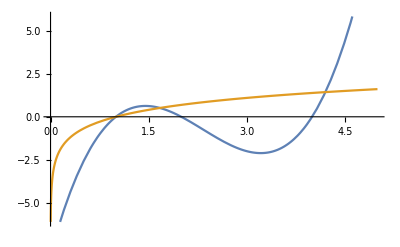

```mathematica
Plot[{x^3-7 x^2+14x - 8, Log[x]}, {x, 0,5}]
```

```mathematica
FindRoot[x^3-7 x^2+14x - 8== Log[x],{x,5}]
```

{x→4.20343}

## 5.5

#### Вариант 9 | y’’+x^2 y’+3cos^2(x)y=0, y(0)=1, y’(0)=-1 на отрезке x=>{-2,4}

```mathematica
funcy=NDSolve[{y''[x]+x^2 * y'[x] + 3* Cos[x]*y[x]==0,y[0]==1,y'[0]==-1},y,{x,-2,4}]
```

{{y→InterpolatingFunction[…]}}

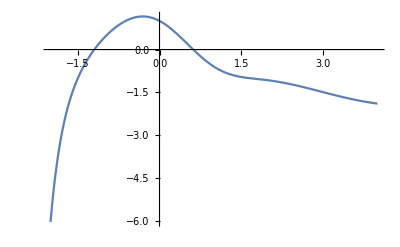

```mathematica
Plot[y[x]/.funcy,{x,-2,4}]
```

#### 5.5.a | Найдите на заданном отрезке корни уравнения y(x)=0

```mathematica
r1=FindRoot[y[x]/.funcy,{x,-1.2}]
```

{x→-1.19731}

```mathematica
r2=FindRoot[y[x]/.funcy,{x,0.6}]
```

{x→0.618748}

#### 5.5.б | Найдите значения производной y’(x) в точках, где y(x)=0

```mathematica
D[y[x]/.funcy,x]/.r1
```

{2.56736}

```mathematica
D[y[x]/.funcy,x]/.r2
```

{-1.83429}

#### 5.5.в | Выберите одну из точек, в которых производная функции y(x)=0, и вычислите значение функции в этой точке

```mathematica
LocalMaxim=FindRoot[D[y[x]/.funcy,x]==0,{x,-1.8}](*Производная равна 0 в точках, где касательная к графику функции паралельна оси абсцисс(точки экстремума)*)
```

{x→-0.307703}

```mathematica
y[x]/.funcy/.LocalMaxim
```

{1.1562}

#### 5.5.г | С помощью функции FindMinimum найдите точки, в которых функция y(x) имеет локальный минимум или максимум, и сравните полученные результаты со значениями, найденными в пункте ‘в’

```mathematica
FindMaximum[y[x]/.funcy,{x,-0.4}]
```

{1.1562,{x→-0.307703}}

## 5.6

#### 5.6.а | Задайте произвольные численные значения параметров a,b,c,d,e в следующих зависимостях: y(x)=a+b*x+c*x^2+d*x^3+e*x^4 и y(x)=a+b*x+c*sin(x)+d*cos(x). Используя функцию Table, определите список численных данных, каждый элемент которого содержит два элемента (x,y). Область изменения х и шаг выберите самостоятельно. С помощью функции Random внесите в каждой точке х случайное возмущение Дy

#### 1)

```mathematica
dat1=Table[{x,(5+2*x+4*x^2+8*x^3+5*x^4)(1+Random[Real,{-0.1,0.1}])},{x,0,5,0.2}]
```

{{0.,4.94924},{0.2,5.33838},{0.4,7.50399},{0.6,10.3367},{0.8,14.1926},{1.,22.5189},{1.2,39.5148},{1.4,54.8932},{1.6,87.9592},{1.8,112.592},{2.,177.626},{2.2,228.476},{2.4,282.225},{2.6,376.945},{2.8,566.437},{3.,695.133},{3.2,902.583},{3.4,1075.96},{3.6,1211.39},{3.8,1623.08},{4.,1878.84},{4.2,2428.96},{4.4,2586.68},{4.6,3023.35},{4.8,3337.34},{5.,4410.13}}

#### 2)

```mathematica
dat2=Table[{x,(15+30*x+52*Sin[x]+8*Cos[x])(1+Random[Real,{-0.1,0.1}])},{x,0,5,0.2}]
```

{{0.,23.4006},{0.2,40.6665},{0.4,59.4267},{0.6,69.091},{0.8,86.7488},{1.,90.4486},{1.2,96.2849},{1.4,106.211},{1.6,104.242},{1.8,127.599},{2.,110.413},{2.2,111.397},{2.4,108.013},{2.6,106.44},{2.8,103.671},{3.,105.195},{3.2,108.056},{3.4,95.641},{3.6,97.1663},{3.8,92.6225},{4.,90.733},{4.2,84.9943},{4.4,98.0492},{4.6,108.397},{4.8,117.187},{5.,116.013}}

#### 5.6.б | Изобразите полученные точки на координатной плоскости

```mathematica
1)
```

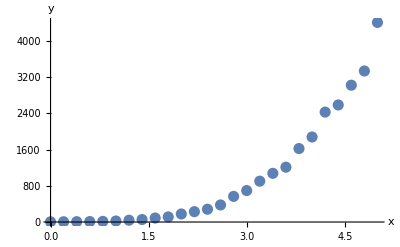

```mathematica
y1=ListPlot[dat1,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
```

```mathematica
2)
```

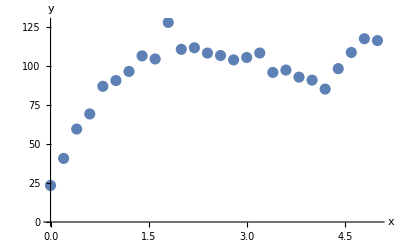

```mathematica
p1=ListPlot[dat2,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
```

#### 5.6.в | С помощью функции Fit найдите наилучшую кривую, аппроксимирующую численные данные

```mathematica
1)
```

```mathematica
apr1=Fit[dat1,{1,x,x^2,x^3,x^4},x]
```

18.3098-61.247 x+55.1112 x^2-4.09972 x^3+5.79095 x^4

```mathematica
apr2=Fit[dat1,{1,x,Sin[x]},x](*экспериментальные точки*)
```

85.8738+393.661 x-859.388 Sin[x]

```mathematica
2)
```

```mathematica
aproc1=Fit[dat2,{1,x,Sin[x],Cos[x]},x]
```

17.7763+29.0591 x+9.06503 Cos[x]+46.7855 Sin[x]

```mathematica
aproc2=Fit[dat2,{1,x,x^2,x^3},x](*экспериментальные точки*)
```

20.0902+112.345 x-43.0027 x^2+4.89582 x^3

#### 5.6.г | На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками

```mathematica
1)
```

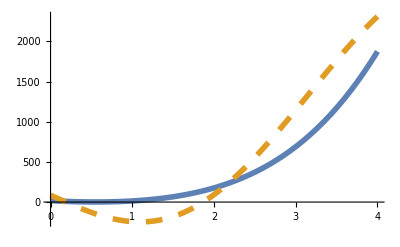

```mathematica
y2=Plot[{apr1,apr2},{x,0,4},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

```mathematica
Show[y1,y2]
```

-Graphics-

```mathematica
2)
```

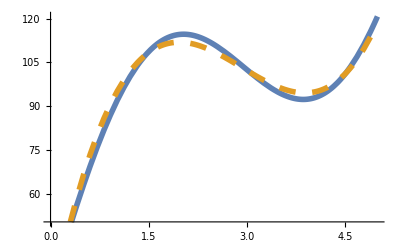

```mathematica
p2=Plot[{aproc1,aproc2},{x,0,5},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

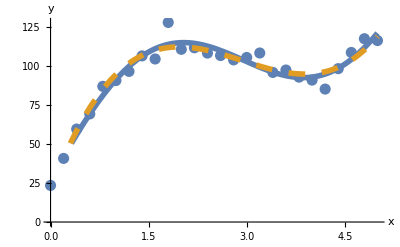

```mathematica
Show[p1,p2]
```